## Sun-Motter PRL 2013 calculations; Problem 14.13

```mathematica
Clear["Global`*"];
```

Condition number of simple chain:  n = 4 case

```mathematica
A4=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}}); B4=({{1}, {0}, {0}, {0}}); ss4=StateSpaceModel[{A4,B4}]; 
wc4=ControllabilityMatrix[ss4];{MatrixForm[wc4],A4.A4//MatrixForm, A4.A4.A4//MatrixForm,
Φ4=MatrixExp[A4 t];  MatrixForm[Φ4]}
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
t | 1 | 0 | 0
t^2/2 | t | 1 | 0
t^3/6 | t^2/2 | t | 1)}

```mathematica
{wg4integrand=Φ4.B4.(Φ4.B4)ᵀ; MatrixForm[wg4integrand],
wg4i=Integrate[wg4integrand,{t,0,τ}]; MatrixForm[wg4i]}
```

{(1 | t | t^2/2 | t^3/6
t | t^2 | t^3/2 | t^4/6
t^2/2 | t^3/2 | t^4/4 | t^5/12
t^3/6 | t^4/6 | t^5/12 | t^6/36),(τ | τ^2/2 | τ^3/6 | τ^4/24
τ^2/2 | τ^3/3 | τ^4/8 | τ^5/30
τ^3/6 | τ^4/8 | τ^5/20 | τ^6/72
τ^4/24 | τ^5/30 | τ^6/72 | τ^7/252)}

```mathematica
eig4=Eigenvalues[wg4i];eig4n=eig4 /.τ->1//N;  Max[eig4n]/Min[eig4n]
```

165823.

Do in function form for defined n

```mathematica
An[n_]:=Table[(KroneckerDelta[i,j+1])1,{i,n},{j,n}];
Bn[n_,q_]:=Flatten[{Table[1,{i,q}],Table[0,{i,n-q}]}];
```

```mathematica
{A5=An[5]; MatrixForm[A5],B5=Bn[5,1]; MatrixForm[B5]}
```

{(0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0),(1
0
0
0
0)}

```mathematica
{Φ5=MatrixExp[A5 t];  MatrixForm[Φ5],
wg5explicit=Integrate[Outer[Times,Φ5.B5,Φ5.B5],{t,0,1}];MatrixForm[wg5explicit]}
```

{(1 | 0 | 0 | 0 | 0
t | 1 | 0 | 0 | 0
t^2/2 | t | 1 | 0 | 0
t^3/6 | t^2/2 | t | 1 | 0
t^4/24 | t^3/6 | t^2/2 | t | 1),(1 | 1/2 | 1/6 | 1/24 | 1/120
1/2 | 1/3 | 1/8 | 1/30 | 1/144
1/6 | 1/8 | 1/20 | 1/72 | 1/336
1/24 | 1/30 | 1/72 | 1/252 | 1/1152
1/120 | 1/144 | 1/336 | 1/1152 | 1/5184)}

```mathematica
γ[n_,t_]:=Module[{wg,eigs,γ0},
wg=Table[t^(i+j-1)/((i+j-1)(i-1)!(j-1)!),{i,n},{j,n}];eigs=Eigenvalues[wg]//N; 
γ0=Max[eigs]/Min[eigs]]
```

```mathematica
γdat=Table[γ[i,1],{i,20}]
```

{1.,19.2815,1181.56,165823.,4.18166×10^7,1.65669×10^10,9.47936×10^12,7.39574×10^15,7.54511×10^18,9.7498×10^21,1.55626×10^25,3.00702×10^28,6.91676×10^31,1.86767×10^35,5.84992×10^38,2.10375×10^42,8.60899×10^45,3.97753×10^49,2.06044×10^53,1.18933×10^57}

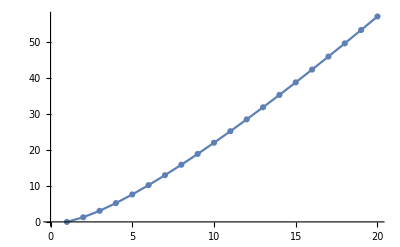

```mathematica
ListLinePlot[Log[10,γdat],PlotMarkers->Automatic]
```

Conclusion:  Even though the Controllability matrix W_c = identity matrix in this example, the controllability Gramian matrix is ill-conditioned as n → ∞

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["chainN.dat",γdat] 
*)
```